```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力(動作に疑問あり) *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
MostOutEdge[PartLoop_,Rank_]:=(
OutEdgeList=DelEleList[Rank,DelEleList[Rank,EdgeNumListVertex[Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]];(* OutEdgeList is Variable *)
OutEdgeList[[1]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝で最もランクが高い枝を出力(動作に疑問あり) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeNumListLine[LineList_]:=EdgeNumListVertex[ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]](* Edge Num List from Line 「Line」のリストから枝番号のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRules[Gout][[EdgeNumListLine[MeshCells[mesh,1]]]](* Edge Rules from Mesh 「MeshRegion」のリストから枝の規則を出力 *)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U)
```

{-6.46748-0.00141247 Area[Polygon[{{25,55},{37,52},{49,49}}]],-4.67823-0.0000202393 Area[Polygon[{{25,55},{37,52},{49,49}}]],3.03224+2.72244×10^-6 Area[Polygon[{{25,55},{37,52},{49,49}}]],-1.61683-7.92085×10^-6 Area[Polygon[{{25,55},{37,52},{49,49}}]],5.94678+0.0000420536 Area[Polygon[{{25,55},{37,52},{49,49}}]],1266,2.51467-0.00114365 Area[Polygon[{{25,55},{37,52},{49,49}}]],8.19991-0.0000204572 Area[Polygon[{{25,55},{37,52},{49,49}}]],-1.1967+0.0000186396 Area[Polygon[{{25,55},{37,52},{49,49}}]],0.167024+0.0000248189 Area[Polygon[{{25,55},{37,52},{49,49}}]]}
 |  |  |  |

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

EdgeRules::graph: EdgeRules[Graph[{If[-6.46748-0.00141247 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],If[-4.67823-0.0000202393 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],«48»,«1225»}]]の位置1にはグラフオブジェクトが想定されています．

VertexList::graph: VertexList[{Graph[{If[-6.46748+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],If[-4.67823+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«47»,If[2.68509+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«1225»}]}]の位置1にはグラフオブジェクトが想定されています．

Part::pkspec1: 式{Graph[{If[-6.46748-0.00141247 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],If[-4.67823-0.0000202393 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],«48»,«1225»}]}は部分指定に使用できません．

EdgeRules::graph: EdgeRules[Graph[{If[-6.46748-0.00141247 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],If[-4.67823-0.0000202393 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],«48»,«1225»}]]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，EdgeRules::graphのこれ以上の出力は表示されません．

VertexList::graph: VertexList[{Graph[{If[-6.46748+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],If[-4.67823+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«47»,If[2.68509+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«1225»}]}]の位置1にはグラフオブジェクトが想定されています．

Part::partw: VertexList[{Graph[{If[-6.46748+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],If[-4.67823+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«47»,If[2.68509+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«1225»}]}]の部分2は存在しません．

Part::pkspec1: 式VertexList[{Graph[{If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],«44»,If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],If[Plus[«2»]>0,Part[«2»]→Part[«2»],Part[«2»]→Part[«2»]],«1225»}]}]⟦2⟧は部分指定に使用できません．

Part::pkspec1: 式{Graph[{If[-6.46748-0.00141247 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],If[-4.67823-0.0000202393 Area[«1»]>0,VertexList[{«1»}]⟦1⟧→VertexList[{«1»}]⟦2⟧,VertexList[{«1»}]⟦2⟧→VertexList[{«1»}]⟦1⟧],«48»,«1225»}]}は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

VertexList::graph: VertexList[{Graph[{If[-6.46748+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],If[-4.67823+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«47»,If[2.68509+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«1225»}]}]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，VertexList::graphのこれ以上の出力は表示されません．

Part::partw: VertexList[{Graph[{If[-6.46748+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],If[-4.67823+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«47»,If[2.68509+Times[«2»]>0,VertexList[«1»]⟦1⟧→VertexList[«1»]⟦2⟧,VertexList[«1»]⟦2⟧→VertexList[«1»]⟦1⟧],«1225»}]}]の部分2は存在しません．

-Graphics-

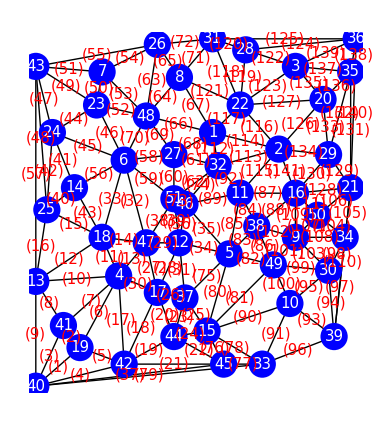

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

19→40 | 19→41 | 40→41 | 40→42 | 19→42 | 4→19 | 4→41 | 13→41 | 13→40 | 4→13
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

4→18 | 13→18 | 4→47 | 18→47 | 18→25 | 13→25 | 4→42 | 17→42 | 42→44 | 17→44
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

42→45 | 44→45 | 37→44 | 15→44 | 15→37 | 17→37 | 17→47 | 12→17 | 12→47 | 4→17
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

12→37 | 6→47 | 6→18 | 5→12 | 5→46 | 12→46 | 40→45 | 47→51 | 12→51 | 14→25
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

14→24 | 24→25 | 14→18 | 23→24 | 6→24
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{(3 √17)/Abs[-6.46748-0.00141247 Area[Polygon[{{25,55},{37,52},{49,49}}]]],1273,(√685)/Abs[0.167024+0.0000248189 Area[Polygon[{{25,55},{37,52},{49,49}}]]]}
 |  |  |  |

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{101,140,86,82,132,116,125,105,64,114,129,104,128,61,115,108,98,111,106,135,67,52,99,84,46,102,23,53,63,68,25,137,136,26,118,40,58,88,127,122,54,74,131,66,130,100,70,120,121,73,24,113,85,80,119,69,126,139,138,20,117,89,50,34,76,56,75,36,2,123,59,81,8,97,77,60,41,133,42,35,45,103,110,124,92,38,16,96,55,5,47,93,9,72,71,14,87,65,3,39,90,12,15,33,107,13,18,22,28,109,4,21,11,43,78,51,37,49,31,95,29,7,79,62,134,83,1,44,112,6,57,10,30,27,48,32,19,91,17,94}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{31/10+√(2/5)+(19 √2)/5+(√(13/5))/2+(√(17/5))/2+7/(√5)+(√(29/5))/2+(√(13/2))/5+3/(√10)+(√13)/5+(√(29/2))/5+(3 √17)/10+(√(41/2))/5+(√(53/2))/5+(√29)/5+(√(73/2))/5+(2 √37)/5+(3 √41)/10+(√(97/2))/5+(√58)/5+(√61)/10+(√73)/5+(√82)/5+(√89)/10+(√101)/5+(√113)/10+(√146)/5+(√173)/10,{1,32,11,38,5,37,17,4,18,47,12,46,51,27,6,48,23,7,43,24,14,25,13,41,40,19,42,44,15,45,33,39,10,49,9,30,34,21,50,16,2,29,20,35,36,3,28,31,26,8,22,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
PartLoop1=PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{2→16,16→29,29→20,20→2}

{20→3,3→22,22→2,2→20}

```mathematica
PartLoopProcess
```

{{2->16,16->29,29->20,20->2}}

{2,20,29,16,2}

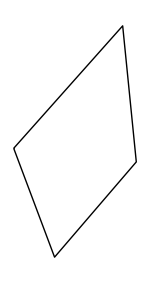

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
MostOutEdge[PartLoop1,PDCurrCostSort]
```

114

```mathematica
OutEdgeList
```

{136,117,122,133,119,137,114,134,139,115,118,113,121,141}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{101,86,82,116,105,64,114,104,128,61,115,108,98,111,106,135,67,52,99,84,46,102,23,53,63,68,25,137,136,26,118,40,58,88,127,122,54,74,131,66,130,100,70,120,121,73,24,113,85,80,119,69,126,139,138,20,117,89,50,34,76,56,75,36,2,123,59,81,8,97,77,60,41,42,35,45,103,110,124,92,38,16,96,55,5,47,93,9,72,71,14,87,65,3,39,90,12,15,33,107,13,18,22,28,109,4,21,11,43,78,51,37,49,31,95,29,7,79,62,134,83,1,44,112,6,57,10,30,27,48,32,19,91,17,94}

```mathematica
PluralPartLoopByGreedyFromRank2[OutEdgeRank[PartLoop1,PDCurrCostSort]]
```

{49→9,9→38,38→49}

```mathematica
FirstPosition[OutEdgeRank[PartLoop1,PDCurrCostSort],55]
```

{84}

```mathematica
EdgeRules[Gout][[OutEdgeRank[PartLoop1,PDCurrCostSort]]]
```

{49→9,38→49,5→49,22→1,34→21,48→8,2→11,34→50,21→29,46→51,22→2,9→34,30→34,1→32,50→21,35→20,8→1,23→48,49→30,11→38,6→23,9→38,37→44,7→48,48→26,1→27,15→37,35→36,35→3,17→37,28→22,14→25,27→6,16→38,16→21,3→22,26→7,32→27,29→35,1→48,21→35,49→10,48→6,8→22,3→28,32→46,44→15,1→2,11→5,15→5,28→31,27→48,20→22,21→36,36→3,44→17,31→22,11→46,23→7,12→5,45→15,6→14,37→5,46→12,41→19,36→28,51→6,49→15,13→41,39→34,45→33,27→51,24→14,25→24,46→5,24→6,30→9,50→16,36→31,11→32,51→47,25→13,33→39,26→43,19→42,43→24,10→39,13→40,31→26,31→8,47→18,11→16,26→8,41→40,51→12,10→15,18→13,18→25,6→18,9→50,47→4,42→17,44→45,17→12,9→16,40→42,42→45,18→4,14→18,33→15,43→7,40→45,43→23,12→37,10→30,12→47,4→41,40→33,27→46,20→3,5→38,19→40,23→24,32→2,4→19,43→13,4→13,4→17,17→47,25→43,47→6,42→44,33→10,42→4,30→39}

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→1,5→4,4→2,1→3,3→5}

{1,2,4,5,3,1}

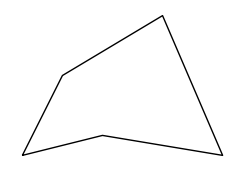

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[line=Line[Pin[[%]]]]
```